```mathematica
Quit[];
```

```mathematica
(*Parameters*)
g=9.81;
T=5;
mass=0.5;
Izz=0.25;
length=0.5;

(*State*)
X={{x[t]},{z[t]},{θ[t]},{x'[t]},{z'[t]},{θ'[t]}};
dX = D[X,t];
U  = {{f1[t]},{f2[t]}};

(*Reference Signal*)
xd[t_]:= Cos[3t]//N;
dxd[t_]:=D[xd[t],t];
zd[t_]:= Sin[3t]//N;
dzd[t_]:= D[zd[t],t];
θd[t_]:= 0;
dθd[t_]:= 0;
f1d[t_]:= 1.5;
f2d[t_]:= 1.5;
Xd[t_]:= {{xd[t]},{zd[t]},{θd[t]},{dxd[t]},{dzd[t]},{dθd[t]}};
Ud[t_]:= {{f1d[t]},{f2d[t]}};




(*Dynamics*)

M[X_]:={{mass,0,0},{0,mass,0},{0,0,Izz}};
G[X_]:= {{0},{-mass*g},{0}};
F[X_]:={{-(U[[1,1]]+U[[2,1]])*Sin[X[[3,1]]]},{-(U[[1,1]]+U[[2,1]])*Cos[X[[3,1]]]},{(U[[2,1]]-U[[1,1]])*length/2}};
TempEq[X_]:=(Inverse[M[X]].(-G[X]+F[X]));

f[X_,U_]:= {{X[[4,1]]},{X[[5,1]]},{X[[6,1]]},{TempEq[X][[1,1]]},{TempEq[X][[2,1]]},{TempEq[X][[3,1]]}};

Subscript[xibar, 0]={Xd[t],{{Ud[t]}}};
Subscript[xi, 0]={{{0},{0},{0},{0},{0},{0}},{{1.5},{1.5}}};

(*Weight matrices*)
Q={{50,0,0,0,0,0},{0, 50,0,0,0,0},{0,0,0.1,0,0,0},{0,0,0,0.001,0,0},{0,0,0,0,0.001,0},{0,0,0,0,0,0.001}};
Subscript[Q, n]=Q;
Subscript[Q, r]=Q;

R={{0.1,0},{0, 0.1}};
Subscript[R, n]=R;
Subscript[R, r]=R;

P1={{50,0,0,0,0,0},{0, 50,0,0,0,0},{0,0,5,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
Subscript[P1, n]=P1;
Subscript[P1, r]=P1;

(*Cost Funtions*)
L[X_,U_]:=1/2((X-Xd[t])ᵀ.Q.(X-Xd[t]))+1/2(U-Ud[t])ᵀ.R.(U-Ud[t]);
J[X_,U_]:=Quiet[NIntegrate[L[X,U],
{t,0,T},Method->{Automatic,"SymbolicProcessing"->False}]]+
1/2((X-Xd[t])/.t->T)ᵀ.P1.((X-Xd[t])/.t->T);
DJzeta[xi_,zeta_]:=
Module[{X=xi[[1]],U=xi[[2]],z=zeta[[1]],v=zeta[[2]]},Return[
Quiet[NIntegrate[(Q.(X-Xd[t]))ᵀ.z+(R.(U-Ud[t]))ᵀ.v,{t,0,T},Method->{Automatic,
"SymbolicProcessing"->False}]]+((P1.(X-Xd[t]))ᵀ.z)/.t->T];
];

(*Symbolic forms of A, B, a, b. Ta transforma A and B to the proper size *)
Asym=D[(f[X,U]),Xᵀ];
Bsym=D[f[X,U],Uᵀ];
asym=D[L[X,U],{X,1}][[1,1]];
bsym=D[L[X,U],{U,1}][[1,1]];
Ta[R_]:=Table[R[[i,1]],{i,1,6}];



(* Riccati solution for P *)
Psol[A_, B_, Q_,R_,P1_]:=Module[{PEQ1, PEQ2, Ps, i, j},
Ri[t_]:=Table[Subscript[P, i,j][t],{i,1,6},{j,1,6}];
PEQ1=
(Ri'[t]+Aᵀ.Ri[t]+Ri[t].A-Ri[t].B.Inverse[R].Bᵀ.Ri[t]+Q)==ConstantArray[0,{6,6}];
PEQ2=Ri[T]==P1;
Ps=(NDSolve[{PEQ1,PEQ2}, Flatten[Ri[t]],{t,0,T},SolveDelayed->True])[[1]];
Return[(Ri[t]/.Ps)];
];

(* Riccati solution for r *)
rsol[A_,B_,a_,b_,P_,R_,P1_,X_]:=Module[{rEQ1,rEQ2,rs},
Rir[t_]:={{r1[t]},{r2[t]},{r3[t]},{r4[t]},{r5[t]},{r6[t]}};
rEQ1=
Rir'[t]+(A-B.Inverse[R].Bᵀ.P)ᵀ.Rir[t]+a-P.B.Inverse[R].b=={{0},{0},{0},{0},{0},{0}};
rEQ2=Rir[T]==(P1.(X-Xd[t]))/.t->T;
rs=(NDSolve[{rEQ1,rEQ2},Flatten[Rir[t]],{t,0,T},Method->{"EquationSimplification"->"Residual"}])[[1]];
Return[(Rir[t]/.rs)];
];

(* Projection of xibar onto feasible space *)
Proj[xibar_,K_]:=Module[{xbar=xibar[[1]], ubar=xibar[[2]], xEQ1, xEQ2,xEQ3,xEQ4, xs},
xEQ1=dX[[4]]==(f[X,U]/.{f1[t]-> (ubar+K.(X-xbar))[[1,1]],f2[t]-> (ubar+K.(X-xbar))[[2,1]]})[[4]];
xEQ2 = dX[[5]]==(f[X,U]/.{f1[t]-> (ubar+K.(X-xbar))[[1,1]],f2[t]-> (ubar+K.(X-xbar))[[2,1]]})[[5]];
xEQ3 = dX[[6]]==(f[X,U]/.{f1[t]-> (ubar+K.(X-xbar))[[1,1]],f2[t]-> (ubar+K.(X-xbar))[[2,1]]})[[6]];
xEQ4={{x[0]},{z[0]},{θ[0]},{x'[0]},{z'[0]},{θ'[0]}}=={{0},{0},{0},{0},{0},{0}};
xs=(NDSolve[{xEQ1,xEQ2,xEQ3,xEQ4},{x[t],z[t],θ[t],x'[t],z'[t],θ'[t]},{t,0,T},Method->{"EquationSimplification"->"Residual"}])[[1]];
Return[(X/.xs)];
];


 (*Descent direction solution*)
zsol[A_,B_,b_,P_,r_]:=Module[{v,zEQ1,zEQ2, zs},
v=-Inverse[Subscript[R, n]].(b+Bᵀ.P.{{z1[t]},{z2[t]},{z3[t]},{z4[t]},{z5[t]},{z6[t]}}+Bᵀ.r);
zEQ1={{z1'[t]},{z2'[t]},{z3'[t]},{z4'[t]},{z5'[t]},{z6'[t]}}==A.{{z1[t]},{z2[t]},{z3[t]},{z4[t]},{z5[t]},{z6[t]}}+B.v;
zEQ2={{z1[0]},{z2[0]},{z3[0]},{z4[0]},{z5[0]},{z6[0]}}==Inverse[P/.t-> 0].(r/.t->  0);
zs=(Quiet[NDSolve[{zEQ1,zEQ2},{z1[t],z2[t],z3[t],z4[t],z5[t],z6[t]},{t,0,T}]])[[1]];
Return[({{z1[t]},{z2[t]},{z3[t]},{z4[t]},{z5[t]},{z6[t]}}/.zs)];
];

(* Armijo line search *)
Armijo[xi_, xibar_, zeta_, K_, maxIters_:30]:=
Module[{α=0.2, β=0.7, n=0, xibarn,γ,X, U, Xn, Un},
X=xi[[1]];
U=xi[[2]];
γ=β^n;
xibarn=xi+γ*zeta;
Xn=Proj[xibarn,K];
Un=xibarn[[2]]+K.(Xn-xibarn[[1]]);
While[
And[(J[Xn,Un])[[1,1]]>(J[X,U]+α*γ*DJzeta[xi,zeta])[[1,1]],n<maxIters],
n=n+1;
γ=β^n;
xibarn=xi+γ*zeta;
Xn=Proj[xibarn,K];
Un=xibarn[[2]]+K.(Xn-xibarn[[1]]);
];
Return[{xibarn,{Xn,Un}}];
];
```

```mathematica
ϵ=10;
i=0;
Subscript[norm, 0]=100;
itercap=5;
(* Full algorithm *)
While[And[Abs[Subscript[norm, i]]>ϵ,i<itercap],
Subscript[A, i]=Ta[Asym]/.{x[t]->Subscript[xi, i][[1,1,1]],
z[t]->Subscript[xi, i][[1,2,1]],θ[t]->Subscript[xi, i][[1,3,1]],x'[t]-> Subscript[xi, i][[1,4,1]],z'[t]-> Subscript[xi, i][[1,5,1]],θ'[t]->Subscript[xi, i][[1,6,1]], f1[t]->Subscript[xi, i][[2,1,1]],f2[t]-> Subscript[xi, i][[2,2,1]]};
Subscript[B, i]=Ta[Bsym]/.{x[t]->Subscript[xi, i][[1,1,1]],
z[t]->Subscript[xi, i][[1,2,1]],θ[t]->Subscript[xi, i][[1,3,1]],x'[t]-> Subscript[xi, i][[1,4,1]],z'[t]-> Subscript[xi, i][[1,5,1]],θ'[t]->Subscript[xi, i][[1,6,1]], f1[t]->Subscript[xi, i][[2,1,1]],f2[t]-> Subscript[xi, i][[2,2,1]]};
Subscript[a, i]=asym/.{x[t]->Subscript[xi, i][[1,1,1]],
z[t]->Subscript[xi, i][[1,2,1]],θ[t]->Subscript[xi, i][[1,3,1]],x'[t]-> Subscript[xi, i][[1,4,1]],z'[t]-> Subscript[xi, i][[1,5,1]],θ'[t]->Subscript[xi, i][[1,6,1]]};
Subscript[b, i]=bsym/.{f1[t]->Subscript[xi, i][[2,1,1]],f2[t]-> Subscript[xi, i][[2,2,1]]};
Subscript[Pn, i]=Psol[Subscript[A, i],Subscript[B, i],Subscript[Q, n],Subscript[R, n],Subscript[P1, n]];
Subscript[r, i]=rsol[Subscript[A, i],Subscript[B, i],Subscript[a, i],Subscript[b, i],Subscript[Pn, i],Subscript[R, n],Subscript[P1, n],Subscript[xi, i][[1]]/.t-> T];
Subscript[z, i]=zsol[Subscript[A, i],Subscript[B, i],Subscript[b, i],Subscript[Pn, i],Subscript[r, i]];
Subscript[v, i]=-Inverse[Subscript[R, n]].(Subscript[b, i]+Subscript[B, i] ᵀ.Subscript[Pn, i].Subscript[z, i]+Subscript[B, i] ᵀ.Subscript[r, i]);
Subscript[zeta, i]={Subscript[z, i],Subscript[v, i]};
Subscript[Pr, i]=Psol[Subscript[A, i],Subscript[B, i],Subscript[Q, r],Subscript[R, r],Subscript[P1, r]];
Subscript[κ, i]=-Inverse[Subscript[R, r]].Subscript[B, i] ᵀ.Subscript[Pr, i];
{Subscript[xibar, i+1],Subscript[xi, i+1]}=Armijo[Subscript[xi, i],Subscript[xibar, i],Subscript[zeta, i],Subscript[κ, i]];
Subscript[norm, i+1]=(DJzeta[Subscript[xi, i],Subscript[zeta, i]])[[1,1]];
i=i+1;

];
```

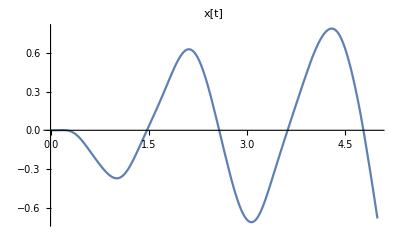

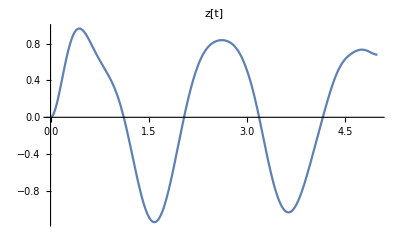

```mathematica
Plot[Subscript[xi, i][[1,1]],{t,0,T},PlotLabel->"x[t]"]
Plot[Subscript[xi, i][[1,2]],{t,0,T},PlotLabel->"z[t]"]
Plot[Subscript[xi, i][[1,3]],{t,0,T},PlotLabel->"θ[t]"]
```

```mathematica
xb=Subscript[xi, i][[1,1,1]];
zb = Subscript[xi, i][[1,2,1]];
θb = Subscript[xi, i][[1,3,1]];

Animate[Graphics[{Blue,Rotate[Rectangle[{(xb/.t-> τ)-length/2,(zb/.t-> τ)-0.05},{(xb/.t-> τ)+length/2,(zb/.t-> τ)+0.05}],θb/.t-> τ]},Axes-> True,AxesLabel->{x,y},PlotRange->{{-2,2},{-2,2}}],{τ,0,T}]

Animate[Graphics[{PointSize[0.05],
Point[{xb/.t-> τ,zb/.t-> τ}]},Axes-> True,AxesLabel->{x,y},PlotRange->{{-2,2},{-2,2}}],{τ,0,T}]
```